This notebook shows how to calculate Doppler broadening for a two-level system using the method outlined in the paper “Exact steady state of perturbed open quantum systems”: https://arxiv.org/abs/2501.06134 and the paper “Fast and Accurate Method for Doppler Averaging of Rydberg EIT Signals”: https://arxiv.org/abs/2501.02141. Screenshots haven been taken from the first paper to help with explaining the code better. Note that the notation in the two papers are different.  

This code generates Fig. 7 in the paper “Exact steady state of perturbed open quantum systems”.

If you use this work for research, we would appreciate citing the papers.

- Omar Nagib* and Thad G. Walker**

*onagib@wisc.edu
**tgwalker@wisc.edu

Install the packages MaTeX and CustomTicks to properly generate the figures:

```mathematica
<<MaTeX`
```

```mathematica
Get["CustomTicks`"]
```

************************************************************************************

Notational definitions

vectorization:  want to represent the N×N density matrix as a N^2 column vector

let v(A)=|A)=∑_ij A_ij i⊗j=∑_ij A_ij i j
Example:  two-level atom ρ=ρ_ee | ρ_eg
ρ_ge | ρ_gg->v(ρ)=ρ_ee
ρ_eg
ρ_ge
ρ_gg

```mathematica
<<Notation`
```

```mathematica
v[A_]:=Flatten[A];
```

Define ⊗ as Kronecker product of x and y:

```mathematica
ClearAll[CircleTimes];

CircleTimes[x_,y_]:=KroneckerProduct[x,y];
```

Define the symbol 𝕀_n as the n by n Identity matrix:

```mathematica
ClearAll[𝕀];
Subscript[𝕀,n_]:=IdentityMatrix[n];
```

Define ᵀ as transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"ᵀ"]]⟹ParsedBoxWrapper[RowBox[{"Transpose","[",x,"]"}]]];
```

Define † as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"†"]]⟹ParsedBoxWrapper[RowBox[{"ConjugateTranspose","[",x,"]"}]]];
```

Define | ⟩ as a column vector, a ket:

```mathematica
ClearAll[Ket];

Ket[v_List]:=Transpose[{Flatten[v]}];
```

Define * as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"*"]]⟹ParsedBoxWrapper[RowBox[{"Conjugate","[",x,"]"}]]];
```

************************************************************************************
Steady state at zero velocity
-Graphics-

Define the Hamiltonian and the Lindblad operators (take ϵ to be real):

```mathematica
h={{-Δ, ϵ/2}, {ϵ/2, 0}};gk={0,1};ek={1,0};Lg=Sqrt[Γ]gk⊗Transpose[ek];
```

-Graphics-

Now construct the Lindbladian (Liouville superoperator), where the formula above can be simplified assuming all operators are real:

```mathematica
ℒ=-ⅈ( h⊗Subscript[𝕀, 2]-Subscript[𝕀, 2]⊗Transpose[h])+( Lg⊗Lg-1/2(Transpose[Lg].Lg⊗Subscript[𝕀, 2])-1/2(Subscript[𝕀, 2]⊗Lgᵀ.Lg)) //Simplify
```

{{-Γ,(ⅈ ϵ)/2,-(ⅈ ϵ)/2,0},{(ⅈ ϵ)/2,-Γ/2+ⅈ Δ,0,-(ⅈ ϵ)/2},{-(ⅈ ϵ)/2,0,-Γ/2-ⅈ Δ,(ⅈ ϵ)/2},{Γ,-(ⅈ ϵ)/2,(ⅈ ϵ)/2,0}}

```mathematica
ℒ//MatrixForm
```

(-Γ | (ⅈ ϵ)/2 | -(ⅈ ϵ)/2 | 0
(ⅈ ϵ)/2 | -Γ/2+ⅈ Δ | 0 | -(ⅈ ϵ)/2
-(ⅈ ϵ)/2 | 0 | -Γ/2-ⅈ Δ | (ⅈ ϵ)/2
Γ | -(ⅈ ϵ)/2 | (ⅈ ϵ)/2 | 0)

To find the steady state, find the nullspace vector to the equation ℒρ=0, which we call ρ∞twolevel:

```mathematica
ρ∞twolevelnull=NullSpace[ℒ]//Flatten
```

{{ϵ^2/(Γ^2+4 Δ^2+ϵ^2)},{-(ⅈ (Γ+2 ⅈ Δ) ϵ)/(Γ^2+4 Δ^2+ϵ^2)},{(ⅈ (Γ-2 ⅈ Δ) ϵ)/(Γ^2+4 Δ^2+ϵ^2)},{1}}

Normalize by dividing the solution by its trace, where the trace is 
-Graphics-

```mathematica
ρ∞twolevel=ρ∞twolevelnull/Tr[v[Subscript[𝕀, 2]]ᵀ.ρ∞twolevelnull]//Simplify
```

{{ϵ^2/(Γ^2+4 Δ^2+2 ϵ^2)},{((-ⅈ Γ+2 Δ) ϵ)/(Γ^2+4 Δ^2+2 ϵ^2)},{((ⅈ Γ+2 Δ) ϵ)/(Γ^2+4 Δ^2+2 ϵ^2)},{1/(1+ϵ^2/(Γ^2+4 Δ^2+ϵ^2))}}

Check that the trace is equal to one, i.e., normalized:

```mathematica
(SuperDagger[v[Subscript[𝕀, 2]]].ρ∞twolevel)//FullSimplify
```

{1}

Find  ρ_eg:

```mathematica
Tr[SuperDagger[v[(ek⊗Transpose[gk])]].ρ∞twolevel]
```

((-ⅈ Γ+2 Δ) ϵ)/(Γ^2+4 Δ^2+2 ϵ^2)

Find  ρ_ge:

```mathematica
Tr[SuperDagger[v[(gk⊗Transpose[ek])]].ρ∞twolevel]
```

((ⅈ Γ+2 Δ) ϵ)/(Γ^2+4 Δ^2+2 ϵ^2)

************************************************************************************
Doppler broadening calculation analytically

Let’s calculate Doppler broadening for ρ_ge analytically first (see screenshot from the paper):
-Graphics-

```mathematica
vt=169.47; (*thermal velocity in μm/μs*)
```

```mathematica
k=1/(.78); (*wavenumber that couples S to Rydberg nP3/2 in microns, .78 is the D2 line*)
ΓRb=6; (*Decay rate of Rb87 in frequency units of MHz*)
```

Here is a plot of the Doppler averaged Im(ρ_eg), which is proportional (up to a multiplicative constant) to the absorption spectrum χ for certain parameters choice:

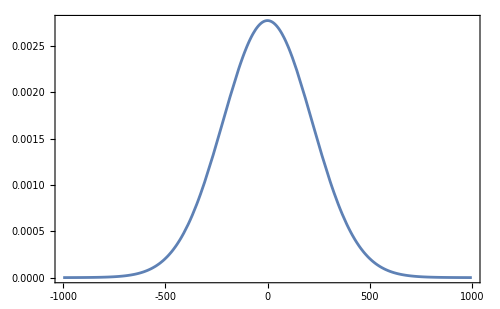

```mathematica
Plot[{(Pi Γ ϵ)/(2Sqrt[Γ^2+2 ϵ^2])PDF[VoigtDistribution[Sqrt[Γ^2+2 ϵ^2]/2,K vT],Δ]/.{Γ->ΓRb,ϵ->1,K->k,vT->vt}},{Δ,-1000,1000},FrameLabel->{MaTeX["\\Delta/2\\pi (\\text{MHz})",Magnification->1.5],MaTeX["\\text{Im}(\\rho_{ge})",Magnification->1.5]},Frame->True,FrameStyle->Directive[GrayLevel[0],17,FontFamily->"Helvetica",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->500,PlotRange->All,Axes->False]
```

************************************************************************************
Doppler broadening calculation with the present method

Summary of the approach below. See the paper for more details about the implementation:

-Graphics-
-Graphics-

Construct ℒ_1:

```mathematica
ℒ1=D[ℒ/.{Γ->gamma0,ϵ->ϵ0,Δ->delta0-K v0},v0]/.{K->k}
```

{{0,0,0,0},{0,0.-1.28205 ⅈ,0,0},{0,0,0.+1.28205 ⅈ,0},{0,0,0,0}}

Define fdopplerArray which acts on a list Λ. A function that is used in the module rhoavg below.

```mathematica
(*Set the function to be Listable so it automatically maps over arrays*)

SetAttributes[fdopplerArray,Listable];

(*Define the function for elements with magnitude less than 10^-3, where we set it to 1 to avoid numrical errors associated with very large/small exponentials. The 10^-3 cutoff is arbitrary and can be changed.*)
fdopplerArray[λ_/;Abs[λ]<10^-3]:=1;

fdopplerArray[Λ_]:=(ⅇ^(-1/(2 Λ^2 vt^2)) √(π/2) (1+Erf[(√(-Λ^2))/(√2 Λ^2 vt)]))/(√(-Λ^2) vt);
```

Important note: 
In the paper, the way the Drazin inverse can be constructed in two ways:

ℒ_0^-=(1/(G_-)R_- ).(L_-)^T (normal version)
-Graphics-

However, Mathematica Eigensystem’s system returns the eigenvectors as rows not columns. Therefore, in the Mathematica implementation we have

ℒ_0^-=(1/(G_-)R_- )^T.L_-   (Mathematica version)

The  second method of construction is:
-Graphics-

```mathematica
Clear[rhoavg]
```

A module that computes the Doppler averaged steady state ρ, using the present approach without any sampling.

```mathematica
rhoavg[delta_,gamma_,epsilon_]:=Module[{delta0=delta,gamma0=gamma,ϵ0=epsilon,v0,vel,L0,L1,ρ∞twolevel0,g,Rg,Lg,λ,rλ,lλ,L0inv,RhoDoppler,P0},

L0=ℒ/.{Γ->gamma0,ϵ->ϵ0,Δ->delta0};(*Initialize Subscript[ℒ, 0] *)


ρ∞twolevel0=ρ∞twolevel/.{Γ->gamma0,ϵ->ϵ0,Δ->delta0};(*Steady state at zero velocity*)

(*method 1: by diagonalization (commented)*)
(*{g,Rg}=Eigensystem[L0];(*Diagonalize ℒ0 to find its right eigenvectors and eigenvalues*)*)
(*Lg=Inverse[Transpose[Rg]];(*Construct the left eigenvectors of Subscript[ℒ, 0] from the right ones*)*)
(*L0inv=Transpose[(1/g[[1;;-2]])Rg[[1;;-2,All]]].Lg[[1;;-2,All]];
(*construct Subscript[ℒ, 0]^- by excluding the zero eigenvector/eigenvalues*)*)
(*method 2: construct the Drazin inverse by direct inversion*)
P0=SparseArray[KroneckerProduct[ρ∞twolevel0,Transpose[v[Subscript[𝕀, Length[h]]]]]];
L0inv=Inverse[L0+P0]-P0;

{λ,rλ}=Eigensystem[L0inv.ℒ1];(*diagonalize Subscript[ℒ, 0]^-Subscript[ℒ, 1] and find its right eigenvectors and eigenvalues*)

lλ=Inverse[Transpose[rλ]];(*construct the left eigenvectors of Subscript[ℒ, 0]^-Subscript[ℒ, 1] directly from rλ*)

RhoDoppler=(Transpose[ fdopplerArray[λ]rλ].lλ).ρ∞twolevel0] (*construct the Doppler averaged steady state*)
```

Now compare the present approach with the analytic formula for the Doppler averaged signal ρ_ge:

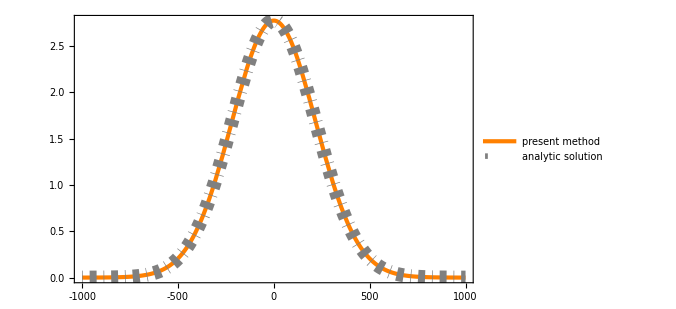

```mathematica
Plot[{10^3*Im[Tr[SuperDagger[v[gk⊗Transpose[ek]]].rhoavg[x,6.,1.]]],((10^3*Pi Γ ϵ)/(2Sqrt[Γ^2+2 ϵ^2])PDF[VoigtDistribution[Sqrt[Γ^2+2 ϵ^2]/2,K vT],x]/.{Γ->6.,ϵ->1,K->k,vT->vt})},{x,-1000,1000},FrameLabel->{MaTeX["\\Delta/2\\pi \ (\\text{MHz})",Magnification->2],MaTeX["\\text{Im}(\\bar{\\rho}_{ge}) (\\times 10^{-3})",Magnification->2]},Frame->True,FrameStyle->Directive[GrayLevel[0],20,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->500,PlotRange->All,Axes->False,PlotLegends->Placed[LineLegend[{"present method","analytic solution"},LegendMarkerSize->{20,10}],{0.79,0.8}],PlotStyle->{Directive[Orange,AbsoluteThickness[3]],Directive[Gray,DotDashed,AbsoluteThickness[10]]},LabelStyle->{FontSize->18,FontFamily->"Times New Roman"}]
```

The two methods are in agreement, as expected. Note that the present approach gives the exact averaged Doppler signal, without any sampling.